```mathematica
(***  This Mathematica Notebook has all the functions and modules necessary to compute the Characteristic Functions (exact and near-exact), and the near-exact PDFs and CDFs for the Linear Combination of Chi-square r.v.s in Section 4 of the book chapter "On the Distribution of Linear Combinations of Chi-Square Random Variables"

Important modules for the user are:
Delta, CompLinCombChiSq, NeCFLinCombChiSq, NePFFLinCombChiSq and NeCDFLinCombChiSq, which compute the measure 'Delta', and the near-exact CF, PDF and CDF
***)

$MaxExtraPrecision = 500;

Rat[x_]:=Module[{nn},
If [ToString[Head[x]]≠"Real",x,
nn=StringLength[ToString[x,InputForm]]-1;Round[x*10^nn]/10^nn]]

SetAttributes[Rat,Listable]

(***  GIG  ***)

Makec[r_,l_,p_]:=Module[{c},
c=Table[Table[1,{j,1,Max[r]}],{i,1,p}];
Do[c[[i,r[[i]]]]=Product[(l[[j]]-l[[i]])^(-r[[j]]),{j,1,i-1}]*Product[(l[[j]]-l[[i]])^(-r[[j]]),{j,i+1,p}]/(r[[i]]-1)!,{i,1,p}];
Do[Do[c[[i,r[[i]]-k]]=Sum[((r[[i]]-k+j-1)!*(Sum[r[[h]]/(l[[i]]-l[[h]])^j,{h,1,i-1}]+Sum[r[[h]]/(l[[i]]-l[[h]])^j,{h,i+1,p}])*c[[i]][[r[[i]]-(k-j)]])/(r[[i]]-k-1)!,{j,1,k}]/k,{k,1,r[[i]]-1}],{i,1,p}];
c]

GIGpdf[r_,li_,zi_,prec_:150]:=Module[{p,l,c,z},
If[Count[r,_Integer]==Length[r]&&And@@NonNegative[r]&&And@@Positive[li]&&Length[r]==Length[li],
If[zi>0,
p=Length[r];l=Rat[li];c=Makec[r,l,p];z=Rat[zi];
SetPrecision[Product[l[[j]]^r[[j]],{j,1,p}]*Sum[Sum[c[[j]][[k]]*z^(k-1),{k,1,r[[j]]}]*Exp[-l[[j]]*z],{j,1,p}],prec],If[zi==0,0,Print["Third argument must be a non-negative value"]]]]]

GIGcdf[r_,li_,zi_,prec_:150]:=Module[{p,l,c,z},
If[Count[r,_Integer]==Length[r]&&And@@NonNegative[r]&&And@@Positive[li]&&Length[r]==Length[li],
If[zi>0,
p=Length[r];l=Rat[li];c=Makec[r,l,p];z=Rat[zi];
1-Product[l[[j]]^r[[j]],{j,1,p}]*SetPrecision[Sum[Sum[c[[j]][[k]]*(k-1)!*Sum[z^i/(i!*l[[j]]^(k-i)),{i,0,k-1}],{k,1,r[[j]]}]*Exp[-l[[j]]*z],{j,1,p}],prec],If[zi==0,0,Print["Third argument must be a non-negative value"]]]]]

(***  GNIG   ***)

Hgeo[b_,k_,x_]:=Module[{F11,F12,F21,F22,F31,F32,res,gg,gg2,rr},
F11=1;
F12=0;
F21=0;
F22=b;
res=Table[0,{j,1,k}];
rr=Re[(-x)^(-b)*(Gamma[b]-Gamma[b,-x])];
res[[1]]=b*rr;
Do[
{F31=(b+j)/(x*j)*((x+b+j-1)*F21-(b+j-1)*F11);
F32=(b+j)/(x*j)*((x+b+j-1)*F22-(b+j-1)*F12);
F11=F21;
F12=F22;
F21=F31;
F22=F32;
res[[j+1]]=F31*Exp[x]+F32*rr},{j,1,k-1}];
res
]

GNIGpdf[r_,bb_,l_,aa_,ww_,prec_:150] := Module[{g,P,a,b,ll,c,w},
 If[Count[r,_Integer]==Length[r] && And@@NonNegative[r] && And@@Positive[l],
If[ww>0,
g = Length[r];
w=Rat[ww];
ll=Rat[l];
a=Rat[aa];
b=Rat[bb];
c =Makec[r,ll,g];
resn=SetPrecision[Table[Hgeo[b,r[[j]],-(a-ll[[j]])*w],{j,1,g}],prec];
SetPrecision[Product[ll[[j]]^r[[j]], {j, 1, g}]*a^b*Sum[Exp[-ll[[j]]*w]*Sum[c[[j]][[k]]*
         Gamma[k]/Gamma[k+b]*w^(k+b-1)*resn[[j,k]],
         {k,1,r[[j]]}],{j, 1, g}],prec],If[ww==0,0,Print["The running value has to be a non-negative value"]]]
 ] ]

GNIGcdf[r_,bb_,l_,aa_,ww_,prec_:150] := Module[{g,P,a,b,ll,c,w},
If[Count[r,_Integer]==Length[r] && And@@NonNegative[r] && And@@Positive[l],
If[ww>0,
g = Length[r];
w=Rat[ww];
ll=Rat[l];
a=Rat[aa];
b=Rat[bb];
c = Makec[r,ll,g];
resn=SetPrecision[Table[Hgeo[b,r[[j]],-(a-ll[[j]])*w],{j,1,g}],prec];
SetPrecision[a^b*w^b/Gamma[b+1]*Hypergeometric1F1[b,b+1,-a w]-Product[ll[[j]]^r[[j]], {j, 1, g}]*a^b*Sum[Exp[-ll[[j]]*w]*Sum[c[[j]][[k]]/ll[[j]]^k*(k-1)!*
    Sum[w^(b+i)*ll[[j]]^i/Gamma[b+1+i]*
         resn[[j,i+1]],{i,0,k-1}],{k,1,r[[j]]}],
         {j, 1, g}],prec],If[ww==0,0,Print["The running value has to be a non-negative value"]]]
 ] ]

(*  CF of a general mixture of Gammas  *)

CFGMG[p_,r_,m_,t_]:=Module[{},
c=Length[p];
pp=Sum[p[[j]],{j,1,c}];
Sum[p[[j]]*m[[j]]^r[[j]]*(m[[j]]-I*t)^(-r[[j]]),{j,1,c}]+(1-pp)*m[[1+c]]^r[[1+c]]*(m[[1+c]]-I*t)^(-r[[1+c]])
]

(*  moments of a general mixture of Gammas  *)

MomGMG[p_,r_,m_,h_]:=Module[{c,pp},
c=Length[p];
pp=Sum[p[[j]],{j,1,c}];
Sum[p[[j]]/m[[j]]^h*Product[(r[[j]]+i),{i,0,h-1}],{j,1,c}]+(1-pp)/m[[1+c]]^h*Product[(r[[1+c]]+i),{i,0,h-1}]
]

(*  Exact CF for a linear combination of chi-squares with weights wj and degrees-of-freedom kj  *)

ExCFLinCombChiSq[wj_,kj_,t_]:=Module[{wjr},If[Length[wj]==Length[kj],wjr=Rat[wj];Product[(1/(2*wjr[[j]]))^(kj[[j]]/2)*(1/(2*wjr[[j]])-I*t)^(-kj[[j]]/2),{j,1,Length[wj]}],Print["Lengths of the weight list and the degrees-of-freedom list do not match"]]]

(*  Exact h-th moment of a linear combination of chi-squares with weights wj and degrees-of-freedom kj  *)

MomLinCombChiSq[wj_,kj_,h_]:=I^(-h)*D[ExCFLinCombChiSq[wj,kj,t],{t,h}]/.t->0

(*  Module for 'previous' computations for the CF, PDF and CDF for a linear combination of chi-squares with weights wj and degrees-of-freedom kj, which matches nm exact moments and which has the rate parameter for the asymptotic part defined by one of the 7 choices in expression (10) in the book chapter, defined by 'ind' (which should be given an integer value between 1 and 7)  *)

CompLinCombChiSq[w_,kj_,nm_,ind_,prec_:250]:=Module[{rjs,wj,mm,p1,r1,r2,pe},
If [MemberQ[Range[1,7],ind], 
{rj=Floor[kj/2];
rjs=kj/2-rj;
rts=Total[rjs];
wj=Rat[w];
lj=1/(2*wj);
p=Length[w];
nmo=nm;
mm=SetPrecision[Table[MomLinCombChiSq[wj,2*rjs,h],{h,1,nm}],prec];
Which[ind==1,lambda=Max[1/(2*wj)],ind==2,lambda=Min[1/(2*wj)],ind==3,lambda=Mean[1/(2*wj)],ind==4,lambda=HarmonicMean[1/(2*wj)],ind==5,lambda=GeometricMean[1/(2*wj)],ind==6,lambda=mm[[1]]/(mm[[2]]-mm[[1]]^2),ind==7,{Clear[p1,r1,r2,lambda];
{p1,r1,r2,lambda}=Cases[{p1,r1,r2,lambda}/.NSolve[Table[mm[[h]]==MomGMG[{p1},{r1,r2},{lambda,lambda},h],{h,1,4}],{p1,r1,r2,lambda}],{_Real,_Real,_Real,_Real}][[1]]}];
Off[Part::partd];
ppp=Flatten[Table[pe[[j]],{j,1,nm}]]/.
Solve[Table[mm[[h]]==MomGMG[Table[pe[[j]],{j,1,nm}],Table[rts+j,{j,0,nm}],Table[lambda,{j,1,nm+1}],h],{h,1,nm}],Flatten[Table[pe[[j]],{j,1,nm}]]][[1]];},Print["Please indicate your choice for the rate parameter of the asymptotic part of the near-exact distribution as an integer number in the range 1-7"]]
]

CompLinCombChiSq::usage="CompLinCombChiSq[w, kj, nm, ind, prec] computes a set of necessary parameters for the near-exact distributions that are necessary for Modules 'NeCFLinCombChiSq', 'NePDFLinCombChiSq' and 'NeCDFLinCombChiSq', which compute the CF, PDF and CDF of the near-exact distributions. It has 5 arguments (from which the first 4 are mandatory): w - the list of 'weights' for each chi-sqaure in the linear combination (which is just a list of values, which do not have to add to 1 and which may have any positive value); kj - list of degrees of freedom for each chi-sqaure in the linear combination; nm - number of exact moments to be matched by the near-exact distributions; ind - an integer value between 1 and 7 indicating the choice for lambda, according to the lsit of choices in expression (10) in section 4 of the
 book chapter; prec - the number of digits to be used in internal computations, with a default value of 250";


NeCFLinCombChiSq[t_]:=Product[lj[[j]]^rj[[j]]*(lj[[j]]-I*t)^(-rj[[j]]),{j,1,p}]*CFGMG[ppp,Table[rts+j,{j,0,nmo}],Table[lambda,{j,0,nmo}],t]

NeCFLinCombChiSq::usage="NeCFLinCombChiSq[t] computes the near-exact characteristic function at 't' for the near-exact distribution last specified with the module 'CompLinCombChiSq', which has to be used before 'NeCFLinCombChiSq'. The only argument for this module is 't', the running value at which the CF is to be computed";

NeCDFLinCombChiSq[z_,prec_:100]:=If[IntegerQ[rts],Sum[ppp[[j+1]]*GIGcdf[Flatten[{rj,rts+j}],Flatten[{lj,lambda}],z,prec],{j,0,nmo-1}]+(1-Total[ppp])*GIGcdf[Flatten[{rj,rts+nmo}],Flatten[{lj,lambda}],z,prec],Sum[ppp[[j+1]]*GNIGcdf[rj,rts+j,lj,lambda,z,prec],{j,0,nmo-1}]+(1-Total[ppp])*GNIGcdf[rj,rts+nmo,lj,lambda,z,prec]]

NeCDFLinCombChiSq::usage="NeCDFLinCombChiSq[z, prec] computes the near-exact CDF for the near-exact distribution last specified with the module 'CompLinCombChiSq', which has to be used before 'NeCDFLinCombChiSq'. The 2 arguments are (only the 1st one is mandatory): z - the running value at which the CDF is to be computed; prec - the number of digits to be used in internal computations, with a default value of 100";

NePDFLinCombChiSq[z_,prec_:100]:=If[IntegerQ[rts],Sum[ppp[[j+1]]*GIGpdf[Flatten[{rj,rts+j}],Flatten[{lj,lambda}],z,prec],{j,0,nmo-1}]+(1-Total[ppp])*GIGpdf[Flatten[{rj,rts+nmo}],Flatten[{lj,lambda}],z,prec],Sum[ppp[[j+1]]*GNIGpdf[rj,rts+j,lj,lambda,z,prec],{j,0,nmo-1}]+(1-Total[ppp])*GNIGpdf[rj,rts+nmo,lj,lambda,z,prec]]

NePDFLinCombChiSq::usage="NePDFLinCombChiSq[z, prec] computes the near-exact PDF for the near-exact distribution last specified with the module 'CompLinCombChiSq', which has to be used before 'NeCDFLinCombChiSq'. The 2 arguments are (only the 1st one is mandatory): z - the running value at which the PDF is to be computed; prec - the number of digits to be used in internal computations, with a default value of 100";

Delta[w_,df_,nm_,ind_,wp_:30,mr_:16,ll_:10^-50,ul_:30000,prec_:250]:=Module[{},
CompLinCombChiSq[w,df,nm,ind];
1/Pi*NIntegrate[Abs[(ExCFLinCombChiSq[w,df,t]-NeCFLinCombChiSq[t])/t],{t,ll,ul},WorkingPrecision->wp,MaxRecursion->mr]]

Delta::usage="Delta[w, df, nm, ind, wp, mr, ll, ul, prec] computes the value of the measure Delta in expression (11) in the book chapter for any near-exact distribution in section 4 of the paper. It has 8 arguments (from which the first 4 are mandatory): w - the list of 'weights' for each chi-sqaure in the linear combination (which is just a list of values, which do not have to add to 1 and which may have any positive value); kj - list of degrees of freedom for each chi-sqaure in the linear combination; nm - number of exact moments to be matched by the near-exact distributions; ind - an integer value between 1 and 7 indicating the choice for lambda, according to the lsit of choices in expression (10) in section 4 of the
 book chapter; wp - the number of working precision digits for the integration (with a default value of 30); mr - the number of maximum recursions for the numerical integration at a given point (default value 16); ll - lower limit for the numerical integration (default value 10^-50); ul - upper limit for the numerical integration (default value 30000); prec - the number of digits to be used in internal computations, with a default value of 250";
```

```mathematica
(* Computing the value for the Delta measure for scenario VIII, 4m and m*=10. The value may be compared with the value in Table 2 in the book chapter for Scenario VIII (4m for m*=10)  *)
```

```mathematica
?Delta
```

Delta[w, df, nm, ind, wp, mr, ll, ul, prec] computes the value of the measure Delta in expression (11) in the book chapter for any near-exact distribution in section 4 of the paper. It has 8 arguments (from which the first 4 are mandatory): w - the list of 'weights' for each chi-sqaure in the linear combination (which is just a list of values, which do not have to add to 1 and which may have any positive value); kj - list of degrees of freedom for each chi-sqaure in the linear combination; nm - number of exact moments to be matched by the near-exact distributions; ind - an integer value between 1 and 7 indicating the choice for lambda, according to the lsit of choices in expression (10) in section 4 of the
 book chapter; wp - the number of working precision digits for the integration (with a default value of 30); mr - the number of maximum recursions for the numerical integration at a given point (default value 16); ll - lower limit for the numerical integration (default value 10^-50); ul - upper limit for the numerical integration (default value 30000); prec - the number of digits to be used in internal computations, with a default value of 250

```mathematica
df={12,17,26,27,29};
w={.43,.29,.18,.13,.11};
Delta[w,df,10,7]
```

1.0773962133561500876129192948×10^-11

```mathematica
(* Computing the PDF and CDF for the case in scenario VIII, 4m and m*=10 *)
(*  Actually, since it is the same near-exact distribution as above, we didn't need to use 'CompLinCombChiSq[w,df,nm,ind]', since it was already implemented inside the module 'Delta'  *)
```

```mathematica
df={12,17,26,27,29};
w={.43,.29,.18,.13,.11};
nm=10;
ind=7;
CompLinCombChiSq[w,df,nm,ind];
z=24.5;
NePDFLinCombChiSq[z]
NeCDFLinCombChiSq[z]
```

0.0704785149471980986617912424715771646493719479916823392343563752982916647898381761653673210370605041

0.827823393314443517636323155814820481564685436706073222866093704079937686181478724265814750038709001

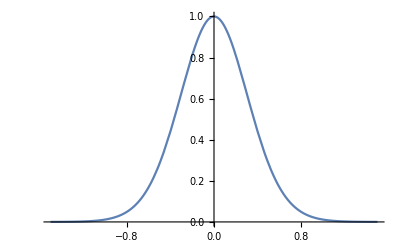

```mathematica
Plot[Abs[NeCFLinCombChiSq[t]],{t,-1.5,1.5},PlotRange->All]
```

```mathematica
(*  This next plot may take an extremely long time to complete  *)
```

```mathematica
Timing[Plot[NePDFLinCombChiSq[z],{z,0,40},PlotRange->All]]
```

```mathematica
(* this version is much faster, although it may take a lttle while to complete *)
```

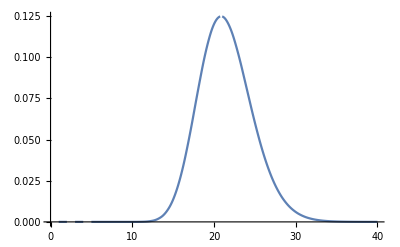

```mathematica
df={12,17,26,27,29};
w={.43,.29,.18,.13,.11};
nm=10;
ind=7;
CompLinCombChiSq[w,df,nm,ind];xx=Table[x,{x,0,40,1}];
yy=Table[NePDFLinCombChiSq[xx[[i]]],{i,1,Length[xx]}];
ListPlot[Table[{xx[[i]],yy[[i]]},{i,1,Length[xx]}],Joined->True,InterpolationOrder->2]
```